Variational Quantum Classifier: Iris

Amplitude Embedding: Methodpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1429043704 | Quantum Circuit Layerpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#75111769
Datapaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1388635064 | Optimizationpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1684028550

This demonstration is a translation of the tutorial “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier” in PennyLane by Maria Schuld. It demonstrates variational quantum classifiers; that is, quantum circuits that can be trained from labelled data to classify new data samples.

In particular, we will see how to encode real vectors as amplitude vectors (amplitude encoding) and train the model to recognize the first two classes of flowers in the Iris dataset.

AmplitudeEmbeddingpaclet:QuantumMob/Q3/ref/AmplitudeEmbeddingQuantumMob Package Symbol | Encodes data into amplitudes of a quantum state
AmplitudeEmbeddingGatepaclet:QuantumMob/QuantumPlaybook/ref/AmplitudeEmbeddingGateQuantumMob Package Symbol | Quantum circuit model to implement amplitude embedding
FindMinimumpaclet:ref/FindMinimum | Find the minimum of a function

Frequently used function in variational classification.

Make sure to load the Q3 package:

```mathematica
Needs["QuantumMob`Q3`"]
```

Amplitude Embedding: Method

```mathematica
Let[Qubit,S]
```

```mathematica
$n=2;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

{S_(,,1),S_(,,2)}

Get the data:

```mathematica
SeedRandom[4312];
```

```mathematica
aa=Normalize@RandomReal[{0,1},$N]
```

{0.570628,0.481167,0.566768,0.348764}

Embed the data into a quantum state:

```mathematica
op=AmplitudeEncoding[aa,SS]
```

AmplitudeEncoding[{0.570628,0.481167,0.566768,0.348764},{S_(,,1),S_(,,2)}]

```mathematica
in=op**Ket[]
```

0.570628 0_(,,S_(,,1))0_(,,S_(,,2))+(0.481167+0. ⅈ) 0_(,,S_(,,1))1_(,,S_(,,2))+(0.566768+0. ⅈ) 1_(,,S_(,,1))0_(,,S_(,,2))+(0.348764+0. ⅈ) 1_(,,S_(,,1))1_(,,S_(,,2))

### Quantum circuit implementation

Embedding the data into a quantum state as above on actual quantum computer is not trivial. One implementation based on quantum circuit model may be achieved by the following function.

```mathematica
QuantumCircuit[op]
```

-Graphics-

More explicitly, the above quantum circuit is equivalent to the following:

```mathematica
QuantumCircuit[UnfoldAll@op]
```

-Graphics-

The above quantum circuit may be further simplified:

```mathematica
qc=QuantumCircuit[GateFactor/@Unfold@op]
```

-Graphics-

```mathematica
new=qc**Ket[SS]//Chop
```

0.570628 0_(,,S_(,,1))0_(,,S_(,,2))+0.481167 0_(,,S_(,,1))1_(,,S_(,,2))+0.566768 1_(,,S_(,,1))0_(,,S_(,,2))+0.348764 1_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
Fidelity[new,in,SS]
```

1.

Data

### Data loading and embedding

Import the iris date and check the first three entries:

```mathematica
raw=Import[PacletObject["QuantumMob/QuantumPlaybook"]["AssetLocation","Iris"],"Table"];
raw=Map[Most[#]->Round[Last@#]&,raw];
raw[[;;3]]
```

{{0.399999999999999911,0.75,0.199999999999999956,0.0500000000000000028}→-1,{0.300000000000000267,0.5,0.199999999999999956,0.0500000000000000028}→-1,{0.200000000000000178,0.600000000000000089,0.150000000000000022,0.0500000000000000028}→-1}

Renormalize the data:

```mathematica
data=Thread[Map[Normalize@Join[Take[#,2],0.3{1,0}]&,Keys@raw]->Values[raw]];
data[[1]]
```

{0.44376,0.83205,0.33282,0.}→-1

Here, vector representation is nothing but the input data itself since we just simulate the amplitude embedding.

```mathematica
(*
in=AmplitudeEncoding[#,SS]&/@Keys[data]//Chop;
in=Matrix[in,SS];
*)
$in=Keys[data];
```

### Features

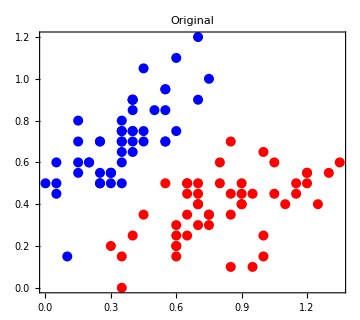

```mathematica
gg=Map[Take[#,2]&,GroupBy[raw,Last,Map[First]],{2}];
Graphics[{PointSize[0.02],Red,Point/@gg[1],Blue,Point/@gg[-1]},
PlotLabel->"Original",
ImageSize->Medium,
Frame->True]
```

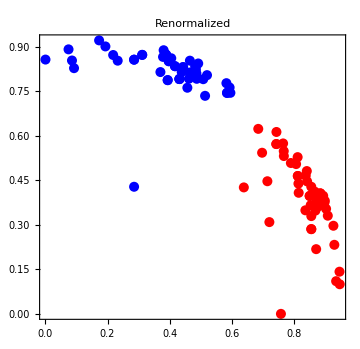

```mathematica
gg=Map[Take[#,2]&,GroupBy[data,Last,Map[First]],{2}];
Graphics[{PointSize[0.02],Red,Point/@gg[1],Blue,Point/@gg[-1]},
PlotLabel->"Renormalized",
ImageSize->Medium,
Frame->True]
```

```mathematica
RR=AmplitudeEncoding[#,SS]&/@Keys[data][[;;,;;-2]];
RR=List@@@Map[UnfoldAll,Unfold/@RR,{2}]/.{CNOT->Nothing};
angles=Map[RotationAngle,RR, {2}];
```

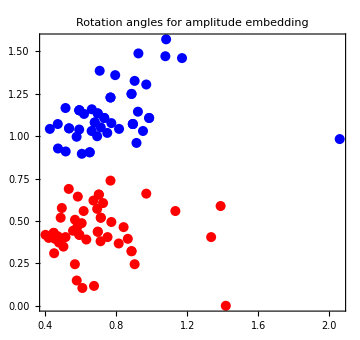

```mathematica
tf=Positive[Values@data]//Flatten;
aa=Pick[angles[[;;,;;2]],tf];
bb=Pick[angles[[;;,;;2]],Not/@tf];
Graphics[{PointSize[0.02],Red,Point/@aa,Blue,Point/@bb},
PlotLabel->"Rotation angles for amplitude embedding",
ImageSize->Medium,
Frame->True]
```

Quantum Circuit Layer

Construct the basic quantum circuit layer to use:

```mathematica
Let[Real,w]
```

```mathematica
layer[lyr_Integer]:=QuantumCircuit[
Table[EulerRotation[w[lyr,k,{1,2,3}],S[k,$]],{k,$n}],
CNOT[S[1],S[2]]
]
layer[ll:{__Integer}]:=Apply[QuantumCircuit,layer/@ll]
```

Check it by show two layers:

```mathematica
layer[{1,2}]
```

-Graphics-

Optimization

### Using three layers

```mathematica
$L=3;
$layer=layer[Range@$L]
$mat=Normal@Matrix[$layer,SS];
```

-Graphics-

```mathematica
ww=w[Range@$L,Range@$n,{1,2,3}];
constraints=Thread[0<=ww<Pi];
```

```mathematica
w0=Flatten@RandomReal[{0,1}*Pi,{$L,$n,3}];
```

```mathematica
Z1=Matrix[S[1,3],SS];
```

```mathematica
Clear[optimizer]
optimizer[w0_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
yy=Part[Values@data,ii];
vv=Transpose@Part[$in,ii];
vv=Transpose[$mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{ww,w0},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[ww/.sol]
]
```

```mathematica
optimizer[w0]
```

1.41881

{avg, yy, cost}  {{-0.987533,0.471648,-0.782469,-0.993516},{-1,1,-1,-1},0.0365607}

{1.41108,1.31963,0.600912,0.571974,2.09734,2.1941,3.00647,1.96685,1.59196,1.04067,2.39685,3.05781,1.02997,0.738747,2.09427,2.43982,1.55341,0.789796}

Find the optimal values of the parameters iteratively.

```mathematica
$R=5;(* the number of iterations *)
new=Nest[optimizer,w0,$R]
```

2.98744

{avg, yy, cost}  {{0.634307,-0.937127,-0.999698,-0.892749},{1,-1,-1,-1},0.017964}

1.56105

{avg, yy, cost}  {{-0.612251,0.478371,-0.592312,0.680273},{-1,1,-1,1},0.167443}

1.28264

{avg, yy, cost}  {{0.950243,0.927384,-0.0774706,0.950243},{1,1,-1,1},0.0748924}

1.59142

{avg, yy, cost}  {{0.879952,0.997978,0.819674,-0.176935},{1,1,1,-1},0.0791663}

2.97221

{avg, yy, cost}  {{0.189552,-0.916977,-0.982924,-0.916977},{1,-1,-1,-1},0.0616988}

{1.00873,1.57982,1.31908,1.66866,2.08633,0.204471,1.85008,2.87359,0.839675,0.206913,1.74532,2.54114,1.49304,1.54739,1.59526,1.74153,1.56363,1.41985}

From the optimized parameters, make predictions:

```mathematica
mm=$mat/.Thread[ww->new];
```

```mathematica
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,-1,1,1,-1,1,-1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,1,1,-1,1,-1,-1,1,-1,-1,-1,-1,1,-1,-1}

```mathematica
predicted-Values[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-2,-2,-2,0,-2,0,-2,0,0,-2,0,-2,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,0,0,-2,0,-2,-2,0,-2,-2,-2,-2,0,-2,-2}

### Using five layers

```mathematica
$L=5;
$layer=layer[Range@$L]
$mat=Normal@Matrix[$layer,SS];
```

-Graphics-

```mathematica
ww=w[Range@$L,Range@$n,{1,2,3}];
constraints=Thread[0<=ww<Pi];
```

```mathematica
w0=Flatten@RandomReal[{0,1}*Pi,{$L,$n,3}];
```

```mathematica
Z1=Matrix[S[1,3],SS];
```

```mathematica
Clear[optimizer]
optimizer[w0_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
yy=Part[Values@data,ii];
vv=Transpose@Part[$in,ii];
vv=Transpose[$mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{ww,w0},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[ww/.sol]
]
```

```mathematica
optimizer[w0]
```

16.3118

{avg, yy, cost}  {{-0.573528,-0.50954,0.469934,0.579281},{-1,-1,1,1},0.218023}

{1.28317,2.92825,0.723176,1.20963,1.15552,0.405018,1.08689,1.49066,0.424001,1.75393,1.30786,2.91821,1.73498,1.53091,2.09897,0.145791,1.16313,1.23217,2.52758,0.830213,2.455,0.978044,1.48463,2.62434,2.33394,0.0949064,1.22597,0.770422,2.33198,1.52989}

Find the optimal values of the parameters iteratively:

```mathematica
$R=5;(* the number of iterations *)
new=Nest[optimizer,w0,$R]
```

14.0798

{avg, yy, cost}  {{0.994189,-0.102732,0.677347,0.988042},{1,-1,1,1},0.0957423}

26.9162

{avg, yy, cost}  {{-0.996964,-0.798403,-0.112775,-0.949484},{-1,-1,1,-1},0.116951}

32.8785

{avg, yy, cost}  {{-0.409258,0.736942,-0.694998,0.302006},{-1,1,-1,1},0.215481}

13.3956

{avg, yy, cost}  {{-0.902952,0.116407,-0.957892,-0.96039},{-1,1,-1,-1},0.0705379}

10.4669

{avg, yy, cost}  {{0.744035,-0.728472,0.564659,-0.585221},{1,-1,1,-1},0.118614}

{1.54055,1.86921,0.791204,1.75254,1.98819,0.870139,1.95517,1.82153,1.10656,1.06307,1.5074,1.77802,2.54321,0.940003,2.59343,0.795141,1.38793,1.25981,2.40863,1.32639,2.61383,0.8774,1.53705,2.25608,2.08004,0.713289,1.65144,1.03877,2.0787,1.54268}

From the optimized parameters, make predictions:

```mathematica
mm=$mat/.Thread[ww->new];
```

```mathematica
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
predicted-Values[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3

| Related Links
Maria Should, PennyLane demonstration “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier”.
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).